## myPackage

```mathematica
(*erstellt am 20##-##-##*)
CloudGet[
 CloudObject[
  "https://www.wolframcloud.com/obj/firlecarl/myPackageWL.wl"]]
  
myFontSize=13
myFontStandard="Lucida Sans Unicode"

myStyle["Wolfram Mathematica Version 14.2",22,Background->Yellow]
(*myColorFavorits = TableForm[Table[ColorData[i],{i,{3,24,35,61,97,106,114}}]]
Table[ContourPlot[x+Sin[x^2+y^2],{x,-4,4},{y,-4,4},Contours->9,ContourShading->ColorData[i,"ColorList"]],{i,{3,24,35,61,97,106,114}}]

myColorGradientFavorits=Table[DensityPlot[y+Sin[x^2+3y],{x,-3,3},{y,-3,3},ColorFunction->ColorData[i]],{i,{"RedBlueTones","Rainbow","DarkRainbow","DarkBands","BrightBands","CMYKColors","Pastel","GrayTones"}}]

Table[ColorData[i,"Image"],{i,{"DarkRainbow","Pastel"}}]*)

myColors=ColorData[61]
myColorForGradient=ColorData["DarkRainbow"]
myCMYKColors[]
myBAUAColors[4]

myExportFigureList={};
myExportEquationList={};

impPath = Directory[] ~~ "\\Desktop\\Quelle\\" (*Import-Pfad anpassen*)
exPath = Directory[] ~~ "\\Desktop\\Ausgabe\\" (*Export-Pfad anpassen*)

pathSaveVersions = 
 Directory[] ~~ "\\Desktop\\Versionsverlauf\\" (*Pfad für Versionsverlauf*)
NotebookOpen[
 CloudObject[
  "https://www.wolframcloud.com/obj/firlecarl/Versionsverlauf.nb"]]

myPackageInputPrint[]
```

13

Lucida Sans Unicode

Wolfram Mathematica Version 14.2

ColorDataFunction[…]

ColorDataFunction[…]

{CMYKColor[{0, 0, 1, 0}],CMYKColor[{Rational[9, 10], Rational[1, 5], Rational[1, 2], 0}],CMYKColor[{0, Rational[3, 5], 1, 0}],CMYKColor[{1, Rational[11, 20], 0, 0}],CMYKColor[{0, Rational[9, 10], 1, 0}],CMYKColor[0, 0.09, 1, 0.03],CMYKColor[{Rational[9, 20], 0, Rational[1, 5], 0}],CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],CMYKColor[{Rational[9, 10], Rational[2, 5], 0, 0}],CMYKColor[{Rational[1, 10], Rational[1, 10], Rational[9, 10], 0}],CMYKColor[{Rational[7, 20], Rational[3, 10], Rational[1, 5], Rational[1, 5]}],CMYKColor[{Rational[7, 10], 0, Rational[19, 20], 0}],CMYKColor[{0, Rational[1, 5], Rational[2, 5], Rational[1, 10]}],CMYKColor[{0, Rational[11, 20], Rational[1, 4], 0}],CMYKColor[{1, Rational[9, 10], 0, Rational[1, 2]}],CMYKColor[{0, Rational[3, 10], 1, 0}],CMYKColor[{Rational[1, 5], Rational[1, 10], Rational[1, 5], Rational[2, 5]}],CMYKColor[{Rational[1, 10], 1, 1, Rational[1, 5]}],CMYKColor[{Rational[3, 5], Rational[9, 10], 0, 0}],CMYKColor[{0, Rational[1, 20], Rational[3, 20], Rational[1, 20]}],CMYKColor[{Rational[4, 5], Rational[1, 10], Rational[4, 5], Rational[2, 5]}],CMYKColor[{0, Rational[9, 10], Rational[9, 10], Rational[1, 5]}],CMYKColor[{1, Rational[2, 5], 0, 0}],CMYKColor[{0, Rational[3, 5], Rational[1, 10], 0}],CMYKColor[{0, Rational[1, 5], Rational[1, 5], Rational[19, 20]}],CMYKColor[{0, Rational[9, 20], 1, 0}],CMYKColor[{Rational[4, 5], Rational[9, 10], 0, 0}],CMYKColor[{0, Rational[1, 5], Rational[1, 2], Rational[1, 5]}],CMYKColor[{Rational[1, 5], 1, 1, Rational[1, 10]}],CMYKColor[{Rational[3, 10], 0, Rational[9, 10], Rational[2, 5]}],CMYKColor[{Rational[99, 100], Rational[13, 25], Rational[1, 25], 0}],CMYKColor[{0, Rational[7, 10], Rational[9, 10], 0}],CMYKColor[{0, 1, 0, 0}],CMYKColor[{Rational[1, 2], Rational[9, 10], 0, Rational[1, 20]}]}

{RGBColor[0.10196078431372549, 0.4392156862745098, 0.7215686274509804],RGBColor[0.38823529411764707, 0.38823529411764707, 0.3843137254901961],RGBColor[0.9568627450980393, 0.9529411764705882, 0.9254901960784314],RGBColor[0.8901960784313725, 0.8980392156862745, 0.8588235294117647],RGBColor[0.6705882352941176, 0.8196078431372549, 0.5607843137254902],RGBColor[0.4588235294117647, 0.7450980392156863, 0.9176470588235294],RGBColor[0.9254901960784314, 0.4, 0.09019607843137255],RGBColor[0.9450980392156862, 0.7019607843137254, 0.],RGBColor[0.6705882352941176, 0.8196078431372549, 0.5607843137254902],RGBColor[0.06666666666666667, 0.3058823529411765, 0.5058823529411764],RGBColor[0.00392156862745098, 0.3607843137254902, 0.5764705882352941],RGBColor[0.6509803921568628, 0.8196078431372549, 0.9450980392156862],RGBColor[0.8117647058823529, 0.8980392156862745, 0.9725490196078431]}

C:\Users\mona_\Desktop\Quelle\

C:\Users\mona_\Desktop\Ausgabe\

C:\Users\mona_\Desktop\Versionsverlauf\

myAroundString[l_List/;Dimensions[l]⟦2⟧==2]:=Module[{},(StringJoin[ToString[#1⟦1⟧]~~ ± ~~ToString[#1⟦-1⟧]]&)/@l]
myBAUAColors[a_Integer:5]:=Module[{bauaMainColors,bauaHighlightColors,bauaBlueColors,bauaAllColors,bauaDesignColors,bauaCMYKColors},{bauaMainColors→{RGBColor[#1A70B8],RGBColor[#636362],RGBColor[#F4F3EC],RGBColor[#E3E5DB],RGBColor[#ABD18F]},bauaHighlightColors→{RGBColor[#EC6617],RGBColor[#75BEEA],RGBColor[#ABD18F],RGBColor[#F1B300]},bauaBlueColors→{{RGBColor[#114e81],RGBColor[#015c93],RGBColor[#1770b8],RGBColor[#74bdea],RGBColor[#a6d1f1],RGBColor[#cfe5f8]}},bauaAllColors→{RGBColor[#1A70B8],RGBColor[#636362],RGBColor[#F4F3EC],RGBColor[#E3E5DB],RGBColor[#ABD18F],RGBColor[#75BEEA],RGBColor[#EC6617],RGBColor[#F1B300],RGBColor[#ABD18F],RGBColor[#114e81],RGBColor[#015c93],RGBColor[#a6d1f1],RGBColor[#cfe5f8]},bauaDesignColors→{RGBColor[0.4588235294117647, 0.7450980392156863, 0.9176470588235294],RGBColor[0.9254901960784314, 0.4, 0.09019607843137255],RGBColor[0.6705882352941176, 0.8196078431372549, 0.5607843137254902],RGBColor[0.9450980392156862, 0.7019607843137254, 0.],RGBColor[0.10196078431372549, 0.4392156862745098, 0.7215686274509804],RGBColor[0.38823529411764707, 0.38823529411764707, 0.3843137254901961],RGBColor[0.8901960784313725, 0.8980392156862745, 0.8588235294117647],RGBColor[0.8117647058823529, 0.8980392156862745, 0.9725490196078431],RGBColor[0.06666666666666667, 0.3058823529411765, 0.5058823529411764]},bauaCMYKColors→{CMYKColor[0.85, 0.5, 0, 0],CMYKColor[0.85, 0.5, 0, 0, 0.7],CMYKColor[0.85, 0.5, 0, 0, 0.4],CMYKColor[0.85, 0.45, 0, 0.3],CMYKColor[0.85, 0.5, 0, 0.4],CMYKColor[0.85, 0.45, 0, 0.3, 0.7],CMYKColor[0.85, 0.45, 0, 0.3, 0.5],CMYKColor[0.85, 0.45, 0, 0.3, 0.3],CMYKColor[0., 0., 0, 0.75],CMYKColor[0., 0., 0.05, 0.06],CMYKColor[0.08, 0.03, 0.12, 0.07],CMYKColor[0.62, 0.27, 0.92, 0.7],CMYKColor[0.55, 0.1, 0, 0],CMYKColor[0., 0.75, 1, 0],CMYKColor[0., 0.3, 1, 0.05],CMYKColor[0.4, 0., 0.55, 0]}}⟦a,2⟧]
myCMYKColors[a_Integer:1]:=Module[{},{{CMYKColor[{0, 0, 1, 0}],CMYKColor[{Rational[9, 10], Rational[1, 5], Rational[1, 2], 0}],CMYKColor[{0, Rational[3, 5], 1, 0}],CMYKColor[{1, Rational[11, 20], 0, 0}],CMYKColor[{0, Rational[9, 10], 1, 0}],CMYKColor[0, 0.09, 1, 0.03],CMYKColor[{Rational[9, 20], 0, Rational[1, 5], 0}],CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],CMYKColor[{Rational[9, 10], Rational[2, 5], 0, 0}],CMYKColor[{Rational[1, 10], Rational[1, 10], Rational[9, 10], 0}],CMYKColor[{Rational[7, 20], Rational[3, 10], Rational[1, 5], Rational[1, 5]}],CMYKColor[{Rational[7, 10], 0, Rational[19, 20], 0}],CMYKColor[{0, Rational[1, 5], Rational[2, 5], Rational[1, 10]}],CMYKColor[{0, Rational[11, 20], Rational[1, 4], 0}],CMYKColor[{1, Rational[9, 10], 0, Rational[1, 2]}],CMYKColor[{0, Rational[3, 10], 1, 0}],CMYKColor[{Rational[1, 5], Rational[1, 10], Rational[1, 5], Rational[2, 5]}],CMYKColor[{Rational[1, 10], 1, 1, Rational[1, 5]}],CMYKColor[{Rational[3, 5], Rational[9, 10], 0, 0}],CMYKColor[{0, Rational[1, 20], Rational[3, 20], Rational[1, 20]}],CMYKColor[{Rational[4, 5], Rational[1, 10], Rational[4, 5], Rational[2, 5]}],CMYKColor[{0, Rational[9, 10], Rational[9, 10], Rational[1, 5]}],CMYKColor[{1, Rational[2, 5], 0, 0}],CMYKColor[{0, Rational[3, 5], Rational[1, 10], 0}],CMYKColor[{0, Rational[1, 5], Rational[1, 5], Rational[19, 20]}],CMYKColor[{0, Rational[9, 20], 1, 0}],CMYKColor[{Rational[4, 5], Rational[9, 10], 0, 0}],CMYKColor[{0, Rational[1, 5], Rational[1, 2], Rational[1, 5]}],CMYKColor[{Rational[1, 5], 1, 1, Rational[1, 10]}],CMYKColor[{Rational[3, 10], 0, Rational[9, 10], Rational[2, 5]}],CMYKColor[{Rational[99, 100], Rational[13, 25], Rational[1, 25], 0}],CMYKColor[{0, Rational[7, 10], Rational[9, 10], 0}],CMYKColor[{0, 1, 0, 0}],CMYKColor[{Rational[1, 2], Rational[9, 10], 0, Rational[1, 20]}]},{Leuchtgelb→CMYKColor[{0, 0, 1, 0}],Zitronengelb→CMYKColor[{Rational[1, 10], Rational[1, 10], Rational[9, 10], 0}],Orange→CMYKColor[{0, Rational[11, 20], 1, 0}],Hellrosa→CMYKColor[{Rational[1, 20], Rational[2, 5], Rational[1, 5], 0}],Altrosa→CMYKColor[{0, Rational[3, 5], Rational[1, 10], 0}],Feuerrot→CMYKColor[{0, 1, 1, Rational[1, 5]}],Signalrot→CMYKColor[{Rational[1, 5], 1, 1, Rational[1, 10]}],Korallenrot→CMYKColor[{0, Rational[9, 10], Rational[9, 10], Rational[1, 5]}],Leuchtrot→CMYKColor[{0, Rational[9, 10], 1, 0}],Reines Rot→CMYKColor[{0, 1, Rational[9, 10], 0}],Weinrot→CMYKColor[{Rational[7, 20], 1, Rational[13, 20], 0}],Pink→CMYKColor[{0, 1, 0, 0}],Lila→CMYKColor[{Rational[1, 2], Rational[3, 5], 0, 0}],Violett→CMYKColor[{Rational[3, 5], Rational[9, 10], 0, Rational[1, 10]}],Azurblau→CMYKColor[{Rational[99, 100], Rational[13, 25], Rational[1, 25], 0}],Himmelblau→CMYKColor[{Rational[9, 10], Rational[2, 5], 0, 0}],Reines Blau→CMYKColor[{1, Rational[7, 10], 0, 0}],Nachtblau→CMYKColor[{1, Rational[9, 10], 0, Rational[1, 2]}],Pastelltürkis→CMYKColor[{Rational[3, 5], Rational[1, 10], Rational[1, 2], 0}],Minttürkis→CMYKColor[{Rational[9, 10], Rational[1, 5], Rational[1, 2], 0}],Türkis→CMYKColor[{Rational[9, 10], Rational[1, 10], Rational[2, 5], Rational[1, 10]}],Leuchtgrün/Gelbgrün→CMYKColor[{Rational[7, 10], 0, Rational[19, 20], 0}],Grün→CMYKColor[{Rational[9, 10], 0, Rational[4, 5], 0}],Grasgrün→CMYKColor[{Rational[9, 10], Rational[1, 5], 1, Rational[1, 4]}],Maigrün→CMYKColor[{Rational[4, 5], Rational[1, 5], 1, Rational[1, 10]}],Rotbraun→CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],Kastanienbraun→CMYKColor[{0, Rational[3, 5], Rational[3, 5], Rational[7, 10]}],Schokobraun→CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],Cremeweiß→CMYKColor[{0, Rational[1, 20], Rational[3, 20], Rational[1, 20]}],Beige→CMYKColor[{0, Rational[1, 5], Rational[2, 5], Rational[1, 10]}],Silbergrau→CMYKColor[{Rational[1, 10], 0, 0, Rational[2, 5]}],Steingrau→CMYKColor[{Rational[1, 5], Rational[1, 10], Rational[1, 5], Rational[2, 5]}],Tiefschwarz→CMYKColor[{Rational[2, 5], Rational[1, 5], Rational[1, 5], 1}]},{Leuchtgelb→{CMYKColor[{0, 0, 1, 0}]},Zitronengelb→{CMYKColor[{Rational[1, 10], Rational[1, 10], Rational[9, 10], 0}]},Orange→{CMYKColor[{0, Rational[3, 10], 1, 0}],CMYKColor[{0, Rational[9, 20], 1, 0}],CMYKColor[{0, Rational[1, 2], 1, 0}],CMYKColor[{0, Rational[11, 20], 1, 0}],CMYKColor[{0, Rational[3, 5], 1, 0}],CMYKColor[{0, Rational[13, 20], 1, 0}],CMYKColor[{0, Rational[7, 10], Rational[9, 10], 0}]},Hellrosa→{CMYKColor[{Rational[1, 20], Rational[2, 5], Rational[1, 5], 0}],CMYKColor[{0, Rational[1, 2], Rational[1, 5], Rational[1, 10]}]},Altrosa→{CMYKColor[{0, Rational[11, 20], Rational[1, 4], 0}],CMYKColor[{0, Rational[3, 5], Rational[1, 10], 0}],CMYKColor[{0, Rational[7, 10], Rational[3, 10], Rational[1, 10]}],CMYKColor[{0, Rational[13, 20], Rational[2, 5], Rational[1, 10]}]},Feuerrot→{CMYKColor[{0, 1, 1, Rational[1, 5]}],CMYKColor[{Rational[1, 10], 1, 1, Rational[1, 5]}]},Signalrot→{CMYKColor[{Rational[1, 5], 1, 1, Rational[1, 10]}],CMYKColor[{Rational[1, 5], 1, Rational[9, 10], Rational[1, 10]}]},Korallenrot→{CMYKColor[{0, Rational[9, 10], Rational[9, 10], Rational[1, 5]}],CMYKColor[{0, Rational[9, 10], Rational[9, 10], Rational[3, 10]}]},Leuchtrot→{CMYKColor[{0, Rational[9, 10], 1, 0}],CMYKColor[{0, 1, 1, 0}]},Reines Rot→{CMYKColor[{0, 1, Rational[9, 10], 0}],CMYKColor[{0, 1, Rational[7, 10], 0}]},Weinrot→{CMYKColor[{Rational[1, 5], 1, Rational[4, 5], Rational[2, 5]}],CMYKColor[{Rational[2, 5], 1, Rational[3, 5], Rational[2, 5]}],CMYKColor[{Rational[7, 20], 1, Rational[13, 20], 0}],CMYKColor[{Rational[3, 5], 1, Rational[4, 5], 0}]},Pink→{CMYKColor[{0, 1, 0, 0}]},Lila→{CMYKColor[{Rational[1, 2], Rational[3, 5], 0, 0}],CMYKColor[{Rational[3, 5], Rational[7, 10], Rational[1, 20], Rational[1, 10]}]},Violett→{CMYKColor[{Rational[1, 2], Rational[9, 10], 0, Rational[1, 20]}],CMYKColor[{Rational[3, 5], Rational[9, 10], 0, 0}],CMYKColor[{Rational[3, 5], Rational[9, 10], 0, Rational[1, 10]}],CMYKColor[{Rational[4, 5], Rational[9, 10], 0, 0}],CMYKColor[{Rational[3, 5], Rational[9, 10], 0, 0}],CMYKColor[{Rational[9, 10], 1, 0, 0}]},Azurblau→{CMYKColor[{Rational[9, 10], Rational[3, 10], Rational[1, 10], Rational[2, 5]}],CMYKColor[{Rational[9, 10], Rational[2, 5], 0, Rational[3, 10]}],CMYKColor[{Rational[99, 100], Rational[13, 25], Rational[1, 25], 0}]},Himmelblau→{CMYKColor[{Rational[9, 10], Rational[2, 5], 0, 0}],CMYKColor[{Rational[9, 10], Rational[1, 2], 0, 0}],CMYKColor[{1, Rational[3, 10], 0, Rational[1, 10]}],CMYKColor[{1, Rational[2, 5], 0, 0}]},Reines Blau→{CMYKColor[{1, Rational[2, 5], 0, 0}],CMYKColor[{1, Rational[11, 20], 0, 0}],CMYKColor[{1, Rational[7, 10], 0, 0}],CMYKColor[{1, Rational[4, 5], 0, 0}],CMYKColor[{Rational[19, 20], Rational[3, 5], 0, Rational[1, 5]}],CMYKColor[{1, Rational[2, 5], 0, Rational[2, 5]}]},Nachtblau→{CMYKColor[{1, Rational[9, 10], 0, Rational[1, 2]}],CMYKColor[{1, 1, Rational[2, 5], Rational[2, 5]}]},Pastelltürkis→{CMYKColor[{Rational[9, 20], 0, Rational[1, 5], 0}],CMYKColor[{Rational[3, 5], Rational[1, 10], Rational[1, 2], 0}],CMYKColor[{Rational[9, 20], 0, Rational[1, 5], Rational[1, 5]}]},Minttürkis→{CMYKColor[{Rational[4, 5], Rational[1, 5], Rational[1, 2], 0}],CMYKColor[{Rational[7, 10], Rational[3, 20], Rational[1, 2], Rational[1, 5]}],CMYKColor[{Rational[9, 10], Rational[1, 5], Rational[1, 2], 0}]},Türkis→{CMYKColor[{Rational[4, 5], Rational[1, 10], Rational[7, 20], Rational[1, 5]}],CMYKColor[{Rational[9, 10], Rational[1, 10], Rational[2, 5], Rational[1, 10]}]},Leuchtgrün/Gelbgrün→{CMYKColor[{Rational[7, 10], 0, Rational[19, 20], 0}],CMYKColor[{Rational[3, 5], 0, Rational[19, 20], 0}],CMYKColor[{Rational[7, 10], 0, Rational[9, 10], 0}]},Grün→{CMYKColor[{Rational[13, 20], 0, Rational[4, 5], 0}],CMYKColor[{Rational[9, 10], 0, Rational[4, 5], 0}],CMYKColor[{Rational[17, 20], 0, 1, 0}],CMYKColor[{Rational[17, 20], 0, 1, Rational[1, 10]}]},Grasgrün→{CMYKColor[{Rational[3, 5], 0, Rational[9, 10], Rational[1, 10]}],CMYKColor[{Rational[3, 10], 0, Rational[9, 10], Rational[2, 5]}],CMYKColor[{Rational[21, 25], 0, 1, 0}],CMYKColor[{Rational[9, 10], Rational[1, 5], 1, Rational[1, 4]}],CMYKColor[{Rational[7, 10], Rational[1, 10], Rational[4, 5], Rational[2, 5]}],CMYKColor[{Rational[4, 5], Rational[1, 10], Rational[4, 5], Rational[2, 5]}]},Maigrün→{CMYKColor[{Rational[4, 5], Rational[1, 5], 1, Rational[1, 10]}]},Rotbraun→{CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],CMYKColor[{Rational[1, 20], 1, 1, Rational[4, 5]}]},Kastanienbraun→{CMYKColor[{0, Rational[3, 5], Rational[3, 5], Rational[7, 10]}],CMYKColor[{Rational[1, 2], 1, 1, Rational[1, 2]}],CMYKColor[{0, Rational[9, 10], 1, Rational[4, 5]}]},Schokobraun→{CMYKColor[{Rational[2, 5], Rational[9, 10], 1, Rational[1, 2]}],CMYKColor[{0, Rational[3, 5], Rational[9, 10], Rational[4, 5]}],CMYKColor[{Rational[2, 5], Rational[7, 10], Rational[3, 5], Rational[4, 5]}],CMYKColor[{0, Rational[1, 5], Rational[1, 5], Rational[19, 20]}],CMYKColor[{Rational[3, 5], Rational[4, 5], Rational[4, 5], Rational[4, 5]}]},Cremeweiß→{CMYKColor[{0, Rational[1, 20], Rational[3, 20], Rational[1, 20]}]},Beige→{CMYKColor[{0, Rational[1, 5], Rational[2, 5], Rational[1, 10]}],CMYKColor[{0, Rational[1, 5], Rational[1, 2], Rational[1, 5]}]},Silbergrau→{CMYKColor[{Rational[1, 10], 0, 0, Rational[2, 5]}]},Steingrau→{CMYKColor[{Rational[1, 5], Rational[1, 10], Rational[1, 5], Rational[2, 5]}],CMYKColor[{Rational[7, 20], Rational[3, 10], Rational[1, 5], Rational[1, 5]}]},Tiefschwarz→{CMYKColor[{1, Rational[2, 5], Rational[2, 5], Rational[9, 10]}],CMYKColor[{Rational[2, 5], Rational[1, 5], Rational[1, 5], 1}],CMYKColor[{Rational[3, 10], 0, 0, 1}],CMYKColor[{0, Rational[1, 2], Rational[1, 5], 1}]}}}⟦a⟧]
myExportEquations[l_List]:=Module[{id,eq},((id=#1⟦2⟧;eq=#1⟦1⟧;Export[exPath~~\equations\~~id~~.txt,ExportString[eq,{MathML,Expression}]];If[MemberQ[myExportEquationList⟦All,1⟧,id],myExportEquationList=ReplacePart[myExportEquationList,FirstPosition[myExportEquationList⟦All,1⟧,id]⟦1⟧→{id,eq}];,AppendTo[myExportEquationList,{id,eq}]];)&)/@l Export[exPath~~\equations\##1 equation IDs and equations.pdf,Column[(Row[Riffle[{#1⟦1⟧,#1⟦2⟧},	]]&)/@myExportEquationList]];Export[exPath~~\equations\##2 equation IDs.rtf,StringRiffle[Prepend[myExportEquationList⟦All,1⟧,exPath~~\equations\],
]];]
myExportF[l_List]:=Module[{r,g,nameID,name,icon},((g=#1⟦1⟧;nameID=#1⟦2⟧;name=#1⟦3⟧;If[#1⟦5⟧==True,r=600;Table[Export[exPath~~CMYK ~~ToString[r]~~ dpi\~~nameID~~ _ ~~ToString[r]~~ dpi CMYK~~i,ColorConvert[Rasterize[g,ImageResolution→r],CMYK]],{i,{.eps,.png}}],Nothing];r=72;icon=Rasterize[g,ImageResolution→r];Table[Export[exPath~~ToString[i]~~ ~~ToString[r]~~ dpi\~~nameID~~ _ ~~ToString[r]~~ dpi~~i,icon],{i,{.png}}];r=150;Table[Export[exPath~~ToString[i]~~ ~~ToString[r]~~ dpi\~~nameID~~ _ ~~ToString[r]~~ dpi~~i,Rasterize[g,ImageResolution→r]],{i,{.png}}];r=#1⟦4⟧;Table[Export[exPath~~ToString[i]~~ ~~ToString[r]~~ dpi\~~nameID~~ _ ~~ToString[r]~~ dpi~~i,Rasterize[g,ImageResolution→r]],{i,{.png}}];(Table[Export[exPath~~ToString[i]~~\~~nameID~~i,g],{i,{.svg,.eps,.pdf}}]&)/@#1;If[MemberQ[myExportFigureList⟦All,1⟧,nameID],myExportFigureList=ReplacePart[myExportFigureList,FirstPosition[myExportFigureList⟦All,1⟧,nameID]⟦1⟧→{nameID,name,icon}];,AppendTo[myExportFigureList,{nameID,name,icon}]];)&)/@l;Export[exPath~~##1 full names of figure IDs.pdf,Column[Join[{		ID figure name,		_________},(Row[Riffle[{#1⟦1⟧,#1⟦2⟧,#1⟦3⟧},	]]&)/@myExportFigureList]]];Export[exPath~~##2 figure IDs.rtf,StringRiffle[myExportFigureList⟦All,1⟧,
]];]
myExportFPNG[l_List]:=Module[{r,g,name},((g=#1⟦1⟧;name=#1⟦2⟧;r=#1⟦3⟧;Table[Export[exPath~~name~~ ~~ToString[r]~~ dpi~~i,Rasterize[g,ImageResolution→r]],{i,{.png}}])&)/@l]
myExportFSVG[l_List]:=Module[{r,g,name},((g=#1⟦1⟧;name=#1⟦2⟧;(Table[Export[exPath~~name~~i,g],{i,{.svg}}]&)/@#1)&)/@l]
myFlatten[l_List,level_Integer]:=Module[{},Map[Flatten[#1]&,l,{level}]]
myFrameStyle[fontsize_Integer:13,fontfamily_String:Lucida Sans Unicode,color_:GrayLevel[0]]:=Module[{},FrameStyle→Directive[FontSize→fontsize,FontFamily→fontfamily,color]]
myFrameTickStyle[fontsize_Integer:13,fontfamily_String:Lucida Sans Unicode,color_:GrayLevel[0]]:=Module[{},FrameTicksStyle→Directive[FontSize→fontsize,FontFamily→fontfamily,color]]
myLabelStyle[fontsize_Integer:13,fontfamily_String:Lucida Sans Unicode,color_:GrayLevel[0]]:=Module[{},LabelStyle→Directive[FontSize→fontsize,FontFamily→fontfamily,color]]
myLegendAppearance[markersize_Integer:13,fontfamily_String:Lucida Sans Unicode,color_:GrayLevel[0]]:=Module[{},LegendAppearance→{LegendMarkerSize→markersize,FontFamily→fontfamily,color}]
myPackageInputPrint[]:=Module[{l},l=ToExpression/@(Select[Names[Global`*],StringContainsQ[my~~__]]/.{myExportFunctionList→Nothing,myExportFigureList→Nothing,myExportEquationList→Nothing,myFontSize→Nothing,myFontStandard→Nothing,myColors→Nothing,myFigureIDs→Nothing,myColorForGradient→Nothing,myPlotColors→Nothing});TableForm[Definition/@l]]
myPlotSequence[]:=Sequence[ImageSize→Large,Frame→True,myFrameStyle[],myFrameTickStyle[]]
myPlotStyle[opacity_:1,colorList_List:myPlotColors]:=Module[{},PlotStyle→(Directive[Opacity[opacity],#1]&)/@colorList]
myReplaceList[lTarget_List,fReplace_]:=Module[{},(#1→fReplace&)/@lTarget]
myStringJoin[l_List,deli_String:,start_Integer:2,end_Integer:-2,step_Integer:2]:=Module[{},StringJoin[Riffle[ToString/@l,deli,{start,end,step}]]]
myStringSplit[s_String,deli_List]:=Module[{i,out,j},i=1;out=StringSplit[s,deli⟦i⟧];For[j=1,j<Length[deli],j++,i++;out=Map[StringSplit[#1,deli⟦i⟧]&,out,{i-1}]];out]
myStyle[s_,fontsize_Integer:13,fontfamily_String:Lucida Sans Unicode,color_:GrayLevel[0]]:=Module[{},Style[If[StringQ[s],s,ToString[s]],FontSize→fontsize,FontFamily→fontfamily,color]]
mySubJoin[lTarget_List,lInsert_List,pos_Integer:1]:=Module[{},(Insert[lTarget⟦#1⟦2⟧⟧,#1⟦1⟧,pos]&)/@lInsert]
myT[l1_List,l2_List]:=Module[{},Transpose[{l1,l2}]]
myTake[lData_List,lSort_List]:=Module[{outList,dimensionQ},If[Length[Dimensions[lData]]>1,dimensionQ=True,dimensionQ=False];outList=If[dimensionQ===True,(If[Head[#1]===Span,lData⟦All,#1⟧,{lData⟦All,#1⟧}]&)/@lSort,(If[Head[#1]===Span,lData⟦#1⟧,{lData⟦#1⟧}]&)/@lSort];outList=(If[Length[#1]>1,Transpose[#1],#1]&)/@outList;outList=Transpose[Flatten[outList,1]]]
myTickStyle[fontsize_Integer:13,fontfamily_String:Lucida Sans Unicode,color_:GrayLevel[0]]:=Module[{},TicksStyle→Directive[FontSize→fontsize,FontFamily→fontfamily,color]]
myTranspose[lLong_List,lShort_List]:=Module[{},Transpose[{lLong,Table[lShort,Length[lLong]]}]]

## myFigureIDs

```mathematica
IntegerString[#,10,3]&/@Range[50]  (*make the next output cell to an input cell with the variable myFigureIDs myFigureIDs=*)
```

```mathematica
myFigureIDs={"001","002","003","004","005","006","007","008","009","010","011","012","013","014","015","016","017","018","019","020","021","022","023","024","025","026","027","028","029","030","031","032","033","034","035","036","037","038","039","040","041","042","043","044","045","046","047","048","049","050"};
```

## data import

```mathematica
urlHead="https://raw.githubusercontent.com/Carl-Firle/effects-of-mask-wearing-on-human-particle-formation/refs/heads/main/raw-data/";
d=Import[urlHead ~~"2025-06-06/first-test-air-cleaner/11-D_2025-06-06-C.dat","Text"];
d=myStringSplit[StringReplace[d,","->"."],{"\n","\t"}];
d[[16;;-1]]=Flatten[{FromDateString[#[[1]]],ToExpression[#[[2;;-1]]]}]&/@d[[16;;-1]];
```

```mathematica
dProtocol=Import[urlHead ~~"2025-06-06/first-test-air-cleaner/%23testdata_protocol.txt"];
```

```mathematica
protocol=#[[1]]->Quantity[ToExpression[#[[2]]],"Milliseconds"]&/@myStringSplit[dProtocol,{" --- "," :: "}];
protocol=#[[1]]->#[[2]]-Min[Values@protocol]&/@protocol
```

{start time***Fri Jun 13 2025 14:58:41 GMT+0200 (Mitteleuropäische Sommerzeit)→0 ms,airCleaner_Airlock_start→1671 ms,airCleaner_cabin_start→2464 ms,roomAirCondition_start→2656 ms,AS_01_start→3008 ms,AS_02_start→3320 ms,AS_03_start→3510 ms,AS_01_start→6399 ms,mask_order***surgical mask,30, ,FFP2 mask,50, ,none,30, ,FFP2 mask,30, ,surgical mask,50, ,none,50, →14924 ms,randomise_start→14924 ms,mask_type***surgical mask***-→15390 ms,target_respMinVol***30***l/min→15599 ms,measurement_start***surgical mask***30→15774 ms,door_airlock_open→15937 ms,door_airlock_closed→16096 ms,door_cabin_open→16301 ms,subject_in_position→16476 ms,door_cabin_closed→16865 ms,door_airlock_open→17074 ms,door_airlock_closed→17278 ms,airCleaner_cabin_end→17455 ms,load_total***50→17763 ms,load_start***50***Watt→17763 ms,load_total***75→18036 ms,load_increase***25***Watt→18036 ms,load_total***100→18223 ms,load_increase***25***Watt→18223 ms,countdown_start***.1***min→25952 ms,pexa_start→29895 ms,pexa_sample_start→30341 ms,pexa_sample_end→30660 ms,load_total***75→31229 ms,load_decrease***25***Watt→31229 ms,load_total***50→31409 ms,load_decrease***25***Watt→31410 ms,load_total***25→31812 ms,load_decrease***25***Watt→31812 ms,exercise_end→31989 ms,pexa_end→32882 ms,measurement_end→33253 ms,door_cabin_exit_open→33469 ms,subject_exits→33668 ms,airCleaner_airlock_end→34055 ms,door_airlock_open→34404 ms,door_cabin_open→34694 ms,window_opening→34893 ms,window_closing→35091 ms,door_cabin_closed→35270 ms,door_airlock_closed→35440 ms,door_cabin_exit_closed→35627 ms,airCleaner_Airlock_start→35833 ms,airCleaner_cabin_start→36087 ms,next_measurement→36400 ms,door_cabin_exit_open→40976 ms,subject_exits→41123 ms,airCleaner_Airlock_end→41304 ms,roomAirCondition_end→41479 ms,AS_01_end→41642 ms,AS_02_end→42002 ms,AS_03_end→42359 ms,AS_01_name***11f→53599 ms,AS_02_name***→53599 ms,AS_03_name***→53599 ms,yearOfBirth***1955→53599 ms,gender***female→53599 ms,height***→53600 ms,weight***→53600 ms,healthy***1→53600 ms,fever***0→53600 ms,illness***0→53600 ms,surgeries***0→53600 ms,cardiovascular***0→53600 ms,infarction***0→53600 ms,aneurysma***0→53600 ms,pneumothorax***0→53600 ms,dizziness***0→53600 ms,respDisease***0→53600 ms,acuteRespDisease***0→53600 ms,allergies***0→53600 ms,nicotineAbuse***0→53600 ms,medication***0→53600 ms,auscultationHeart***distinct &amp; clear sounds, regular rhythm, normal heart rate, no abnormal sounds→53600 ms,heartRate***→53600 ms,rhythm***SA node→53600 ms,cardiacAxis***normal→53600 ms,heartBlock***none→53600 ms,rWave***regular R-wave progression→53600 ms,repolarisation***none→53601 ms,auscultationLung***vesicular sound, normopnoea, no pathological breath sound→53601 ms,end of protocol→53601 ms}

```mathematica
"AS_01_end"/.protocol
```

41642 ms

```mathematica
tab=ToTabular[d[[16;;-1]],"Rows",<|"ColumnKeys"->d[[15]] /. "[d&t31.12.2035 11:50:55]" -> "time"|>];
tab=CastColumns[%,#->"Quantity"::["Real64","Micrometers"]&/@(sizeRange=d[[15,2;;-1]])];
tab=TransformColumns[tab,{"time"->Function[Round[#time-(tab[[All,"time"]] [[-1]])+UnitConvert["AS_01_end"/. protocol,"Seconds"],.5]]}]
```

```mathematica
Table[Missing[],Length@sizeRange]
```

{Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[]}

```mathematica
temp=tab[[207;;-1]]
```

```mathematica
Dimensions@temp
```

{7,32}

```mathematica
TabularRow[Table[Missing[],Dimensions[temp][[2]]]]
```

TabularRow[…]

```mathematica
Insert[temp,TabularRow[Table[Missing[],Dimensions[temp][[2]]]],3]
```

Insert::ins: Cannot insert at position {3} in Tabular[<7,32>]

Insert[,TabularRow[…],3]

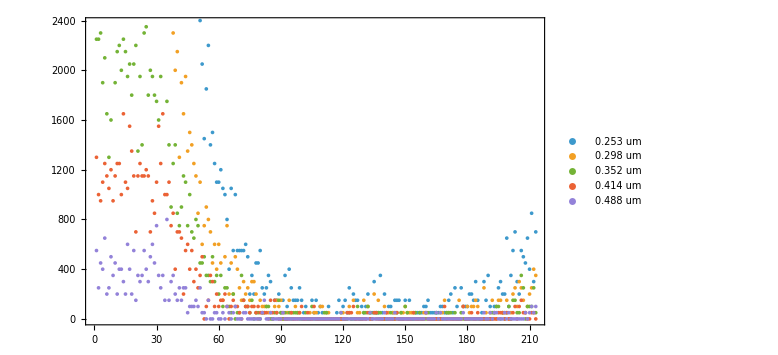

```mathematica
ListPlot[Transpose[Values/@(ConstructColumns[tab,sizeRange[[1;;5]]]//Normal)],myPlotSequence[],PlotLegends->sizeRange[[1;;5]]]
```